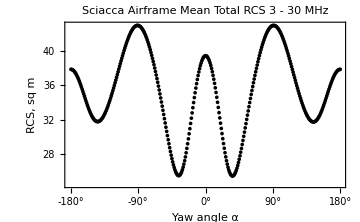

```mathematica
gnew=ListPlot[σ[[17]],
isize,
Frame->True,
FrameTicks->fticks,
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS 3 - 30 MHz",
Joined->False,
PlotStyle->Black]
```

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

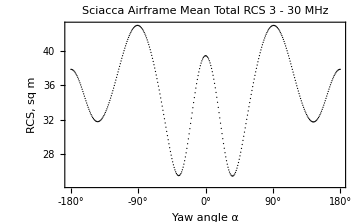

```mathematica
gnew=ListPlot[meanRCS[[1]],
isize,
Frame->True,
FrameTicks->fticks,
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS 3 - 30 MHz",
Joined->False,
PlotStyle->{Black,PointSize[0.0025]}]
```

### increase

```mathematica
title="Sciacca Airframe"<>lf;
Do[
subtitle="Mean Total RCS at 3 - "<>ToString[2+k]<>" MHz";
If[k==1,subtitle="Mean Total RCS at 3 MHz"];
g=ListPlot[meanRCS[[1;;k]],
isize,
Frame->True,
FrameTicks->fticks,
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->title<>subtitle,
PlotRange->{Automatic,{-2,62}},
Joined->False,
PlotStyle->{{Black,PointSize[0.0025]}}];
Export[dirGraph<>"up-"<>pad[k]<>".gif",g];
,{k,28}]
```

### decrease

```mathematica
title="Sciacca Airframe"<>lf;
Do[
subtitle="Mean Total RCS at 30 - "<>ToString[30-k+1]<>" MHz";
If[k==1,subtitle="Mean Total RCS at 30 MHz"];
g=ListPlot[Drop[meanRCS,28-k],
isize,
Frame->True,
FrameTicks->fticks,
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->title<>subtitle,
PlotRange->{Automatic,{-2,62}},
Joined->False,
PlotStyle->{{Black,PointSize[0.0025]}}];
Export[dirGraph<>"down-"<>pad[k]<>".gif",g];
,{k,28}]
```

## imagemagick

```mathematica
f=Table[
" accumulation-decrease-"<>pad[d]
,{d,0,ω}];
b=Table[
" accumulation-decrease-"<>pad[d]
,{d,28}];
a=Join[f,b];
StringReplace[a,","->""]
```

{ data-fit-rcs-cos-00, data-fit-rcs-cos-01, data-fit-rcs-cos-02, data-fit-rcs-cos-03, data-fit-rcs-cos-04, data-fit-rcs-cos-05, data-fit-rcs-cos-06, data-fit-rcs-cos-07, data-fit-rcs-cos-08, data-fit-rcs-cos-09, data-fit-rcs-cos-10, data-fit-rcs-cos-11, data-fit-rcs-cos-12, data-fit-rcs-cos-13, data-fit-rcs-cos-14, data-fit-rcs-cos-15, data-fit-rcs-cos-16, data-fit-rcs-cos-17, data-fit-rcs-cos-18, data-fit-rcs-cos-19, data-fit-rcs-cos-20, data-fit-rcs-cos-21, data-fit-rcs-cos-22, data-fit-rcs-cos-23, data-fit-rcs-cos-24, data-fit-rcs-cos-25}

```mathematica
"convert-delay 20-loop 0*.jpg myimage.gif"
```

convert-delay 20-loop 0*.jpg myimage.gif

```mathematica
stem="convert -delay 40 -loop 0";
Do[
stem=stem<>" down-"<>pad[d]<>".gif"
,{d,28}];
Do[
stem=stem<>" down-"<>pad[d]<>".gif"
,{d,28,1,-1}];
stem=stem<>" nu-decrease.gif"
```

convert -delay 40 -loop 0 down-01.gif down-02.gif down-03.gif down-04.gif down-05.gif down-06.gif down-07.gif down-08.gif down-09.gif down-10.gif down-11.gif down-12.gif down-13.gif down-14.gif down-15.gif down-16.gif down-17.gif down-18.gif down-19.gif down-20.gif down-21.gif down-22.gif down-23.gif down-24.gif down-25.gif down-26.gif down-27.gif down-28.gif down-28.gif down-27.gif down-26.gif down-25.gif down-24.gif down-23.gif down-22.gif down-21.gif down-20.gif down-19.gif down-18.gif down-17.gif down-16.gif down-15.gif down-14.gif down-13.gif down-12.gif down-11.gif down-10.gif down-09.gif down-08.gif down-07.gif down-06.gif down-05.gif down-04.gif down-03.gif down-02.gif down-01.gif nu-decrease.gif

```mathematica
stem="convert -delay 40 -loop 0";
Do[
stem=stem<>" up-"<>pad[d]<>".gif"
,{d,28}];
Do[
stem=stem<>" up-"<>pad[d]<>".gif"
,{d,28,1,-1}];
stem=stem<>" nu-increase.gif"
```

```mathematica
"
```